```mathematica
RegionPlot3D[Subscript[x, 1]^2-Subscript[x, 2]^2-Subscript[x, 3]^2≥1,{Subscript[x, 1],-5,5},{Subscript[x, 2],-5,5},{Subscript[x, 3],-5,5},AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

```mathematica
Subscript[x, 2]=r[t] Cos[ϕ[t]];
Subscript[x, 3]=r[t] Sin[ϕ[t]];
Subscript[xPlus, 1]=√(r[t]^2+a^2);
Subscript[xMinus, 1]=√(r[t]^2+a^2);
$Assumptions={r[t]≥0,r'[t]∈Reals,a>0,ϕ[t]∈Reals,ϕ'[t]∈Reals,m>0};
```

```mathematica
1/2 m Norm[D[{Subscript[xPlus, 1],Subscript[x, 2],Subscript[x, 3]}, t]]^2//FullSimplify
1/2 m Norm[D[{Subscript[xMinus, 1],Subscript[x, 2],Subscript[x, 3]}, t]]^2//FullSimplify
```

1/2 m ((1+r[t]^2/(a^2+r[t]^2)) r'[t]^2+r[t]^2 ϕ'[t]^2)

1/2 m ((1+r[t]^2/(a^2+r[t]^2)) r'[t]^2+r[t]^2 ϕ'[t]^2)

```mathematica
L=1/2 m ((1+r[t]^2/(a^2+r[t]^2)) r'[t]^2+r[t]^2 ϕ'[t]^2);
```

```mathematica
D[L, r'[t]]
```

m (1+r[t]^2/(a^2+r[t]^2)) r'[t]

```mathematica
D[L, ϕ'[t]]
```

m r[t]^2 ϕ'[t]

```mathematica
Solve[{ℒ==1/2 m ((1+r[t]^2/(a^2+r[t]^2)) r'[t]^2+r[t]^2 ϕ'[t]^2),Subscript[p, r]==m (1+r[t]^2/(a^2+r[t]^2)) r'[t],Subscript[p, ϕ]==m r[t]^2 ϕ'[t],H==Subscript[p, r] r'[t]+Subscript[p, ϕ] ϕ'[t]-ℒ},{H,ℒ,r'[t],ϕ'[t]}]//FullSimplify
```

{{H→(((a^2+r[t]^2) p_r^2)/(a^2+2 r[t]^2)+p_ϕ^2/r[t]^2)/(2 m),ℒ→(((a^2+r[t]^2) p_r^2)/(a^2+2 r[t]^2)+p_ϕ^2/r[t]^2)/(2 m),r'[t]→((a^2+r[t]^2) p_r)/(m (a^2+2 r[t]^2)),ϕ'[t]→p_ϕ/(m r[t]^2)}}

```mathematica
ℰ==(((a^2+r[t]^2) Subscript[p, r]^2)/(a^2+2 r[t]^2)+Subscript[p, ϕ]^2/r[t]^2)/(2 m)/.Subscript[p, r]->m (1+r[t]^2/(a^2+r[t]^2)) r'[t]//FullSimplify
```

ℰ==p_ϕ^2/(2 m r[t]^2)+(m (a^2+2 r[t]^2) r'[t]^2)/(2 (a^2+r[t]^2))

```mathematica
Solve[{ℰ==Subscript[p, ϕ]^2/(2 m r[t]^2)+(m (a^2+2 r[t]^2) r'[t]^2)/(2 (a^2+r[t]^2)),Subscript[p, ϕ]==m r[t]^2 ϕ'[t]},{r'[t],ϕ'[t]}]
```

{{r'[t]→-(√(a^2+r[t]^2) √(2 m ℰ r[t]^2-p_ϕ^2))/(√(a^2 m^2 r[t]^2+2 m^2 r[t]^4)),ϕ'[t]→p_ϕ/(m r[t]^2)},{r'[t]→(√(a^2+r[t]^2) √(2 m ℰ r[t]^2-p_ϕ^2))/(√(a^2 m^2 r[t]^2+2 m^2 r[t]^4)),ϕ'[t]→p_ϕ/(m r[t]^2)}}

```mathematica
((√(a^2+r[t]^2) √(2 m ℰ r[t]^2-Subscript[p, ϕ]^2))/(√(a^2 m^2 r[t]^2+2 m^2 r[t]^4)))^2/(Subscript[p, ϕ]/(m r[t]^2))^2/.r[t]->r[ϕ]//FullSimplify
```

(r[ϕ]^2 (a^2+r[ϕ]^2) (2 m ℰ r[ϕ]^2-p_ϕ^2))/((a^2+2 r[ϕ]^2) p_ϕ^2)

```mathematica
DSolve[r'[ϕ]^2==(r[ϕ]^2 (a^2+r[ϕ]^2) (2 m ℰ r[ϕ]^2-Subscript[p, ϕ]^2))/((a^2+2 r[ϕ]^2) Subscript[p, ϕ]^2),r[ϕ],ϕ]
```

```mathematica
sol=NDSolve[{(a^2+2 r[ϕ]^2) Subscript[p, ϕ]^2  r'[ϕ]^2==r[ϕ]^2 (a^2+r[ϕ]^2) (2 m ℰ r[ϕ]^2-Subscript[p, ϕ]^2)/.{a->1,m->1,ℰ->1,Subscript[p, ϕ]->1},r[0]==1},r[ϕ],{ϕ,0,2π}]
```

NDSolve::mxst: Maximum number of 268209 steps reached at the point ϕ == 1.53138.

NDSolve::ndsz: At ϕ == 1.04372, step size is effectively zero; singularity or stiff system suspected.

{{r[ϕ]→InterpolatingFunction[{{0., 1.53138}}, <>][ϕ]},{r[ϕ]→InterpolatingFunction[…][ϕ]}}

```mathematica
Show[RegionPlot3D[Subscript[x, 1]^2-Subscript[x, 2]^2-Subscript[x, 3]^2≥1,{Subscript[x, 2],-5,5},{Subscript[x, 3],-5,5},{Subscript[x, 1],-5,5},AxesLabel->{"x_1","x_2","x_3"},Mesh->None],ParametricPlot3D[{r[ϕ]Cos[ϕ],r[ϕ]Sin[ϕ],√(r[ϕ]^2+1^2)}/.sol[[2]],{ϕ,0,1}],ParametricPlot3D[{r[ϕ]Cos[ϕ],r[ϕ]Sin[ϕ],-√(r[ϕ]^2+1^2)}/.sol[[2]],{ϕ,0,1}]]
```

-Graphics3D-

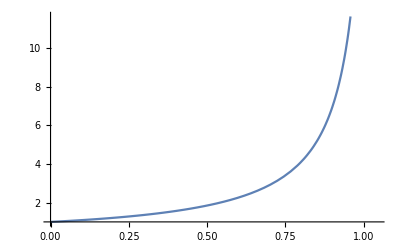

```mathematica
Plot[r[ϕ]/.sol[[2]],{ϕ,0,1.043722}]
```

```mathematica
D[L, ϕ[t]]
```

0

```mathematica
D[L, ϕ'[t]]
```

m r[t]^2 ϕ'[t]

```mathematica
Subscript[p, ϕ]=m r[t]^2 ϕ'[t]
```

```mathematica
DSolve[eqn,{r[t],ϕ[t]},t]
```

DSolve[{r[t] (-a^2 r'[t]^2+(a^2+r[t]^2)^2 ϕ'[t]^2)==(a^2+r[t]^2) (a^2+2 r[t]^2) r''[t],r[t] (2 r'[t] ϕ'[t]+r[t] ϕ''[t])==0},{r[t],ϕ[t]},t]

```mathematica
r'[ϕ]^2==(r[ϕ]^2 (a^2+r[ϕ]^2) (2 m ℰ r[ϕ]^2-Subscript[p, ϕ]^2))/((a^2+2 r[ϕ]^2) Subscript[p, ϕ]^2)
```